-0.0374218-2.29143×10^-18 ⅈ

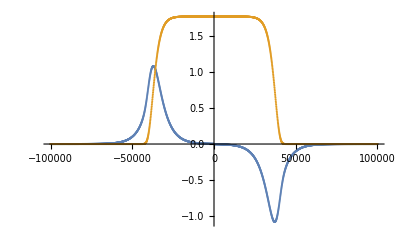

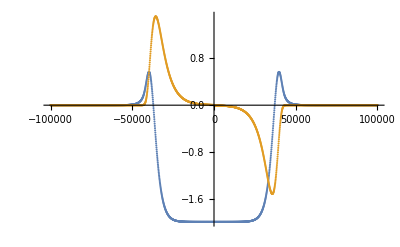

/Users/dg6/code/kineticj/mathematica

```mathematica
(*This form is from pg 406 is Swanson.*)
Z[re_,im_]:= I Sqrt[Pi] Exp[-(re+ I im)^2] Erfc[-I (re+I im)];
Zp[re_,im_]:=-2 (1+(re+I im) Z[re,im]);
(*This is the range and resolution of the file ... recall it's non-uniform resolution*)
argMin=0.001;argMax=100000;argN=1000;
zReNonUniform=N[Table[10^(i/(argN-1)*(Log10[argMax]-Log10[argMin])+Log10[argMin]),{i,0,argN-1}]];
zReNonUniform1=Prepend[zReNonUniform,0];
zReNonUniform2=Join[-Reverse[zReNonUniform],zReNonUniform1];
ZData=Z[zReNonUniform2,0];
ZPData=Zp[zReNonUniform2,0];
Z[26.7411,0]
zReMin=-100000;zReMax=100000;nPtsRe=2000;
(*The above are only for the plotting range now. Use the lines below to specify the non-uniform file range. *)
ListPlot[{Re[ZData],Im[ZData]},DataRange->{zReMin,zReMax}]
ListPlot[{Re[ZPData],Im[ZPData]},DataRange->{zReMin,zReMax}]
SetDirectory["~/code/kineticj/mathematica"]
Export["zFunction.nc",{"arg_re"->zReNonUniform2, "Z_re"->Re[ZData], "Z_im"->Im[ZData], "Zp_re"->Re[ZPData],"Zp_im"->Im[ZPData]}];
```